```mathematica
Integrate[Exp[-t/τ]*(A*Sin[t*ω]^2+B),{t,0,Infinity}]
```

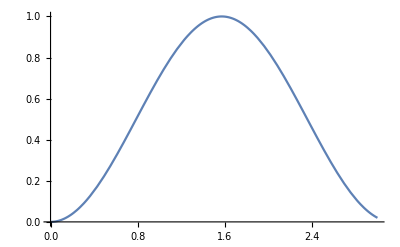

```mathematica
Plot[Sin[x]^2,{x,0,3}]
```

```mathematica
m=1
```

1

```mathematica
Plot[(2 m^2)/((1/g)^3+4 (1/g) m^2),{g,0,0.4}]
```

-Graphics-

```mathematica
ContourPlot3D[(2 m^2)/(g^3+4 g m^2),{g,0,10},{m,0,10}]
```

ContourPlot3D::argrx: ContourPlot3D called with 3 arguments; 4 arguments are expected.

ContourPlot3D[(2 m^2)/(g^3+4 g m^2),{g,0,10},{m,0,10}]

```mathematica
Solve[(2 m^2)/(g^3+4 g m^2) ==Exp[-x*g]*Sin[x*m]^2 , x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

```mathematica
NSolve[(2 m^2)/(g^3+4 g m^2)==ⅇ^(-g x) Sin[m x]^2,x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[(2 m^2)/(g^3+4 g m^2)==ⅇ^(-g x) Sin[m x]^2,x]

```mathematica
++
```

```mathematica
Clear[A,B,ω]
```

```mathematica
Integrate[Exp[-t/τ]/τ*(A*Sin[t*ω]^2+B),{t,0,Infinity}]
```

ConditionalExpression[B+(2 A τ^2 ω^2)/(1+4 τ^2 ω^2),Re[1/τ]>2 Abs[Im[ω]]]

```mathematica
B=1; A= 1; ω = 1;
```

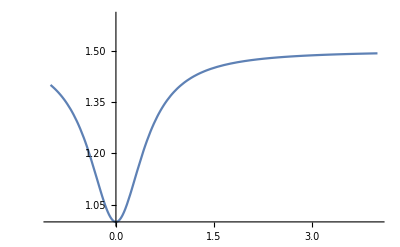

```mathematica
Plot[B+(2 A τ^2 ω^2)/(1+4 τ^2 ω^2),{τ,-1,4}, PlotRange->{Automatic, {1,1.6}}]
```

```mathematica
ts = Table[t /. NSolve[B+(2 A τ^2 ω^2)/(1+4 τ^2 ω^2) == (A*Sin[t*ω]^2+B),t][[2]],{τ,0.05,5,0.1}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

{0.0704179,0.20461,0.321751,0.417525,0.492726,0.550621,0.594953,0.629015,0.655404,0.676069,0.692442,0.705568,0.716212,0.724937,0.732163,0.738203,0.743296,0.747626,0.751335,0.754533,0.757309,0.759733,0.76186,0.763737,0.765401,0.766882,0.768207,0.769395,0.770466,0.771434,0.772311,0.773109,0.773836,0.774502,0.775111,0.775672,0.776188,0.776664,0.777105,0.777513,0.777892,0.778244,0.778572,0.778878,0.779164,0.779432,0.779683,0.779919,0.78014,0.780348}

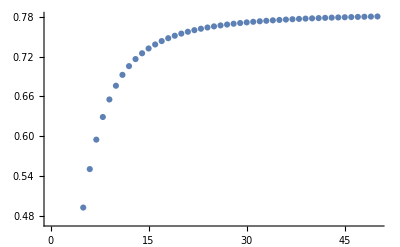

```mathematica
ListPlot[ts]
```